## 2D infinite potential well

### Constants

```mathematica
ℏ=1;
M=1;
```

### Dimensions

```mathematica
a=1;
b=√(π/3);
b//N
```

1.02333

### Spectrum

```mathematica
spectrum[nx_,ny_]:=(ℏ^2 π^2)/(2M) (nx^2/a^2+ny^2/b^2)
```

Required number of states:

```mathematica
Ntotal=100000;
```

Estimated maximum energy (using the semiclassical level density) :

```mathematica
Emax=1.1*Ntotal (2π ℏ^2)/(a b M)
```

675396.

Estimated maximum indices nx, ny :

```mathematica
p=√(Emax (2M)/(π ℏ)^2);
nxmax=Round[p a+1]
nymax=Round[p b+1]
```

371

380

Sorted levels:

```mathematica
energies=Sort[Select[Flatten[Table[spectrum[nx,ny],{nx,1,nxmax},{ny,1,nymax}]],#<Emax&]//N];
energies=energies[[1;;Ntotal]];
```

Streching ("Unfolding") - subtracting the first element and dividing by the last one

```mathematica
unfolded=energies-energies[[1]];
unfolded=unfolded Ntotal/unfolded[[-1]];
```

### Level spacings

```mathematica
spacings=Differences[unfolded];
```

### Histogram

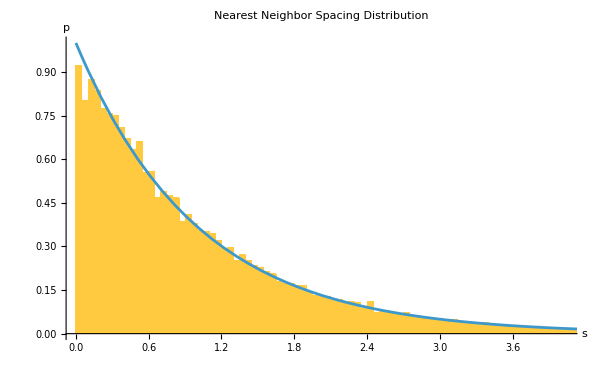

```mathematica
Show[{Histogram[spacings,200,"PDF",PlotLabel->"Nearest Neighbor Spacing Distribution",AxesLabel->{"s","p"}],Plot[Exp[-x],{x,0,5}]}]
```

### Ratios of consecutive spacings

```mathematica
spacings=Differences[energies];
ratios=spacings[[2;;-1]]/spacings[[1;;-2]];
ratiost=If[#>1,1/#,#]&/@ratios;
```

Mean value:

```mathematica
Mean[ratiost]
```

0.390149

Theoretically it should be

```mathematica
2Log[2]-1//N
```

0.386294

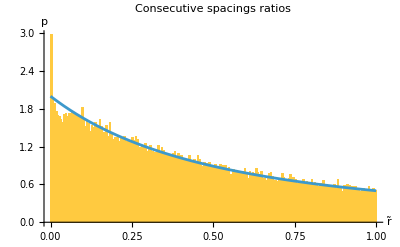

```mathematica
Show[{Histogram[ratiost,200,"PDF",PlotLabel->"Consecutive spacings ratios",AxesLabel->{"r̃","p"}],Plot[2/(1+x)^2,{x,0,1}]}]
```